# Mathematica Tutorial Weston Barger SIAM: March 02, 2017

## What is Mathematica?

### Mathematica is a TERM WRITING system. Given an EXPRESSION as input, Mathematica attempts to perform operations on the EXPRESSION in order to simplify it.

### There are two types of EXPRESSIONS: atoms and normal expressions

#### Atoms: Things like symbols, numbers or strings

```mathematica
a
γ
Γ
7
7.123
"this is a string"
```

#### Normal expressions: all have the form HEAD[PART1, PART2, ... ], where PARTk may be a normal expression or an atom

```mathematica
x^2 
x^2  //FullForm
```

x^2

Power[x,2]

```mathematica
D[x^3,x]
```

3 x^2

```mathematica
FullForm[
Hold[x^2  + D[x^3,x]]
]
```

Hold[Plus[Power[x,2],D[Power[x,3],x]]]

#### We can think of normal expressions in a tree format

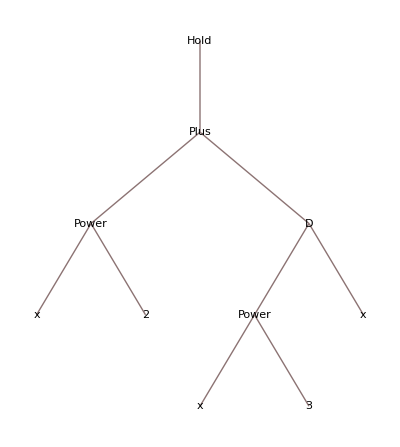

```mathematica
TreeForm[
Hold[x^2  + D[x^3,x]]
]
```

```mathematica
TreeForm[
Hold[x^2]  + D[x^3,x]
]
```

```mathematica
TreeForm[
x^2  + D[x^3,x]
]
```

```mathematica
Trace[  x^2  + D[x^3,x]  ]
```

#### You can use the command Head to peel of the head of the expression Operations like + , *, ^ are all special input forms which correspond to Plus[a,b], Times[a,b], Power[a,b]

```mathematica
TreeForm[ a + b]
```

```mathematica
TreeForm[ a - b]
```

```mathematica
Head[ a - b]
```

```mathematica
TreeForm[a + b + c + d]
```

#### Boolean Operators

```mathematica
7 > 4 && 2 == 3
7 > 4 || 2 == 3
7 ≤  4 || 2≠ 3
```

#### Nested Boolean operators

```mathematica
2 < 3 < 4 < 5 <6 < 7
```

#### When Mathematica can’t tell, it doesn’t evaluate Boolean expressions

```mathematica
a == b
```

#### You want SameQ i.e. ===

```mathematica
SameQ[a,b]
a === b
```

```mathematica
a + b === b + a
```

## Rules and Patterns

### A pattern is a Mathematica expression that represents and entire class of expressions. This most simple pattern in the “Blank” _ , which matches any expression The next most simple pattern is the _Head, which matches any expression

```mathematica
3 a + 4.5 b^2 /. { x_Integer -> x ^2}
```

```mathematica
3 a + 4.5 b^2 /. { x_Symbol -> x ^2}
```

### Patterns have temporary variables. They are called pattern variables.

```mathematica
(f[a] + g[b]) / (f[a,b]) /. { x_f -> x^2}
```

```mathematica
(f[a] + g[b]) / (f[a,b]) /. { f[x_] -> x^2}
```

(a^2+g[b])/f[a,b]

```mathematica
(f[a] + g[b]) / (f[a,b]) /. { f[x_,y_] -> (x^2 - y^2),g[x_] -> x^3}
```

```mathematica
f[a] /. { a -> b}
```

### Why does this happen?

```mathematica
x / Exp[y]  /. { Exp[z_]-> z}
```

### Because all rule replacements are made based on the “FullForm” of the expression

```mathematica
x/ Exp[y] //FullForm
```

### Here, Exp[z_] matches with Times[-1,y]. Example of rule based programming

```mathematica
data = {{x1,y1},{x2,y2}, {x3,y3},{x4,y4}}
```

```mathematica
data /. {  {x_,y_} -> {x,Log[y]}}
```

### Note that the RHS of a rule “ LHS -> RHS” is evaluated before replacement

```mathematica
data /. { {x_,y_} -> {x, RandomReal[]}}
```

### We can get around that by using a RuleDelayed :>

```mathematica
data /. { {x_,y_} :>  {x, RandomReal[]}}
```

## Deconstructing

### A pattern can be constructed from any expression by substituting Blanks “_” .

```mathematica
f[a] + g[b] /. { x_[_] -> x}
```

f+g

```mathematica
f[a] + g[b] /. { x_[_,_] -> x}
f[a] + g[b] //FullForm
```

Plus

Plus[f[a],g[b]]

```mathematica
f[a] + g[b] /. { x_[y_] -> y[x]}
```

a[f]+b[g]

```mathematica
4x + D[f[t],t] + Sup [ 9t] /. { _ + Sup[x_] -> x}
```

### Two useful functions for testing Rules are MatchQ and Cases MatchQ tests the entire expression

```mathematica
{ a, a +b , a + a}//FullForm
```

```mathematica
MatchQ[ { a, a +b , a + a}, _Plus]
```

```mathematica
MatchQ[ { a, a +b , a + a}, _List]
```

```mathematica
MatchQ[ { a, a +b , a + a}, List[_,_]]
```

```mathematica
MatchQ[ { a, a +b , a + a}, List[_,_,_]]
```

### Cases takes a list as it’s first argument and tests each element and returns the ones that match

```mathematica
Cases[ { a, a +b , a + a}, _Plus]
```

```mathematica
Cases[ { a, a +b , a + a}, x_ + y_ -> x^y]
```

{a^b}

### Cases only searches Level 1 of the full expression by default

```mathematica
Cases [ 5 ( a + b)^7, _Integer]
```

{5}

### As an optional third argument we can specify levels of search

```mathematica
Cases [ 5 ( a + b)^7, _Integer,2]
Cases [ 5 ( a + 8 b)^7, _Integer,Infinity]
```

### According to Roman Maeder, one of the designers of Mathematica, pattern matching and rule substitution are “the underlying mechanism for implementing all other programming constructs.”

## Setting values: the operators = (Set) and := (SetDelayed) are used to map values to expressions

### = (Set) evaluates the RHS of the expression then sets

```mathematica
Clear[z,x,y]
```

```mathematica
z = x + y
Trace[z]
```

```mathematica
z / 2
Trace [ z / 2]
```

```mathematica
x = 2;
z
Trace[z]
```

```mathematica
Clear[z]
```

```mathematica
z = x + y
Trace[z]
```

```mathematica
x = 3;
z
Trace[z]
```

#### := (SetDelayed) holds the RHS until the LHS is called, then the RHS is evaluated

```mathematica
Clear[z,y,x]
```

```mathematica
x = 2;
z := x + y
z
```

```mathematica
x = 3;
z
```

```mathematica
Trace[z]
```

```mathematica
z1 = RandomReal[];
z2 := RandomReal[]
```

```mathematica
z1
z2
```

```mathematica
z1
z2
```

### We can think of head[part] like a function call f[x]

```mathematica
Clear[f,x,z,y]
```

```mathematica
f[x]
f @ x
x //f
```

### Function declaration: we need the “Blank” character _

#### This amounts to a replacement rule

```mathematica
f[xvar_,yvar_]:= Sqrt[ xvar] + yvar
```

```mathematica
f[a,b]
```

```mathematica
f[x,y]
```

### We see that functions are really delayed replacement rules

```mathematica
DownValues[ f]
```

#### Without _ , we see that g gets the evaluation we “intended” only when the actual symbols x,y are used as inputs

```mathematica
g[x,y] := Sqrt[x] + y
```

```mathematica
g[a,b]
```

```mathematica
g[x,y]
```

```mathematica
h[1] = 1;
h[2] = 1;
h[n_]:= h[n-1] + h[n-2]
```

```mathematica
h[15]
```

```mathematica
DownValues[h]
```

### Example: Suppose we’d like to specify that an operator A is linear

```mathematica
Clear[A]
A[ Plus[ x_,y__]]:=Plus[A[x], A[Plus[y]]]
```

```mathematica
A[a + b]
A[a + b + c]
DownValues[A]
```

A[a]+A[b]

A[a]+A[b]+A[c]

{HoldPattern[A[x_+y__]]:>A[x]+A[+y]}

## Attributes, OwnValues, DownValues, UpValues

```mathematica
Attributes[Plus]
```

```mathematica
Clear[f]
```

#### Flat: Associative

```mathematica
Attributes[f] = { Flat};
f[  f[ a,b] , c]
```

f[a,b,c]

```mathematica
Attributes[f] = {}
```

#### Orderless: Commutitive

```mathematica
Attributes[f] = {Orderless};
```

```mathematica
f[a,b]
f[b,a]
```

```mathematica
Attributes[f] = {Flat, Orderless};
f[ c,f[a,b]]
```

f[a,b,c]

```mathematica
Attributes[f] = {HoldFirst};
f[ D[x^3,x]]
g[ D[x^3,x] ]
```

#### OwnValues

```mathematica
Attributes[f] = {};
Clear[f,g,h]
```

```mathematica
a = 2;
OwnValues[a]
DownValues[a]
UpValues[a]
```

#### DownValues

```mathematica
f[x_]:= x^2
```

```mathematica
OwnValues[f]
DownValues[f]
UpValues[f]
```

#### UpValues

```mathematica
g /: Plus[ g[x_], 4] := g[x]^4
```

```mathematica
g[6] + 2
g[6] + 4
```

2+g[6]

g[6]^4

```mathematica
OwnValues[g]
DownValues[g]
UpValues[g]
```

## Lists

### Basic data type in Mathematica. Denoted by curly brackets

```mathematica
Clear[f,g,a,h]
mlist = {e1,e2,e3,e4,e5,e6}
mlist//FullForm
```

### Indexed by [[k]], starting at k = 1

```mathematica
mlist[[1]]
```

```mathematica
f[ mlist]
f @ mlist (* Uses entire list as argument *)
f @ mlist //FullForm
```

```mathematica
Apply[f,mlist]
f @@ mlist (* Replaces List head with f *)
f @@ mlist //FullForm
```

```mathematica
Map [ f, mlist]  (* Applies f at each list item *)
f /@ mlist
f /@ mlist //FullForm
```

```mathematica
Solve[ x^2 - x - 6 == 0, x] (* Returns a List of solutions in the form of replacement rules *)
```

### Matrices are lists of lists

```mathematica
IdentityMatrix[5] 
IdentityMatrix[5] //MatrixForm
DiagonalMatrix[{a,b,c,d}] //MatrixForm
```

### Test for list membership

```mathematica
l = { a,b,c,d,e,f}
MemberQ[ l,c]
MemberQ[ l,z]
```

### Can use Length[ _List]

```mathematica
Table[ l[[k]]^2, {k,1,Length[l]}]
```

### Can use Select to filter out a list

```mathematica
l = Range[10]
gtfive[n_]:= n > 5
Select[ l, gtfive]
```

```mathematica
l = {a,{{b,c},{d,e}},{f}}
Flatten[l]
```

```mathematica
Flatten[l,1]
```

## Functional Programming

```mathematica
Clear[f,h,a,g]
```

### Pure functions

```mathematica
Function[x, x^2] [ a]
```

### “Function” is a special Head that tells Mathematica to treat it’s contents as a function. In Python and Lisp, these are called “lambda expressions.” There is shorthand notation using # and &

```mathematica
f = #^2 &;
f[a]
```

### For example, we can use Filter like

```mathematica
Select[ Range[10], 5 < # &]
```

### We can define multiparameter functions like

```mathematica
f = #1^2 + #2^3 &;
f[a,b]
```

### Think of this like operator notation...

```mathematica
h = D[#,t] - (1/2) D[#,{x,2}] &; (* Define the heat operator *)

h @ g[t,x]
```

```mathematica
h @ (  Exp[-t/2] Sin[x]  )
```

### Be careful about orders of operations.

```mathematica
Hold[h @  Exp[-t/2] Sin[x]   ]
```

### When in doubt (which can be often), use parentheses

## Useful functions

## Solve and DSolve

```mathematica
Solve[ x^2 - 4 x+ 3 == 0, x]
```

```mathematica
Solve[ { x + y , x - y} == {1/2, 1/4}, {x,y}]
Solve[  x + y == 1/2 && x - y ==1/4, {x,y}]
```

```mathematica
DSolve[ y'[x] - 9 y[x] == 6 && y[0] == 1,y[x],x]
```

## Differentiation

```mathematica
Clear[f]
```

```mathematica
D[f[x],x]
```

```mathematica
f'[x]
```

```mathematica
D[ Tan[x] Sin[ Pi Exp[ x]],x]
```

#### Derivative at a point x = π

```mathematica
D[ Tan[x] Sin[ Pi Exp[ x]],x] /. {x-> Pi}
```

```mathematica
f[expr_,p_]:= (D[ expr,x] )/. { x-> p}
```

```mathematica
f[ Cos[x] , 1]
```

## Total Differentiation

```mathematica
Clear[f]
```

```mathematica
Dt[  f[y],x]
```

## Integration

```mathematica
Integrate[Sin[x],x]
```

```mathematica
Integrate[ Sin[x]Exp[4x ] - x^4,{x,0,Pi}]
```

## Series (and Normal)

```mathematica
Clear[f,ϵ]
```

```mathematica
Series[ f[x], {x,x0, 3}]
```

```mathematica
Series[ f[x], {x,x0, 3}]//FullForm
```

```mathematica
Series[ f[x], {x,x0, 3}] //Normal
```

```mathematica
Series[ f[x], {x,x0, 3}] //Normal//FullForm
```

### Be careful with multi-variate series expansions, it does them iteratively

```mathematica
Series[ f[x,y], {x,x0,2},{y,y0,2}]//Normal
```

### To get a multivariate Taylor expansion, use the following trick

```mathematica
(Series[ f[x0 + ϵ ( x - x0) ,y0 + ϵ ( y - y0) ], { ϵ, 0, 2}]//Normal )/. { ϵ -> 1}
```

```mathematica
SeriesTwo[fun_,order_Integer,{x_,x0_},{y_,y0_}]:= Normal[ Series[ fun[ x0 + ϵ ( x - x0), y0 + ϵ ( y - y0)],{ϵ,0,order}]]/.{ϵ-> 1}
```

```mathematica
SeriesTwo[ f,3,{x,x0},{z,z0}]
```

## Simplify

```mathematica
expr = D[Integrate[ 1 / ( x^3 + 1),x],x]
```

```mathematica
expr //TreeForm
```

```mathematica
expr =Simplify[ expr]
expr //TreeForm
```

## ExpToTrig / TrigToExp

```mathematica
Cos[ 3 x - 8]Sinh[ 9 y] //TrigToExp
```

```mathematica
( Exp[-x] - Exp[x 9])//ExpToTrig
```

```mathematica
( Exp[-x] - Exp[x 9])//ExpToTrig//Simplify
```

```mathematica
( Exp[-x] - Exp[x 9])//ExpToTrig//FullSimplify
```

## Applications

## Change of variables

### Black Scholes PDE

```mathematica
bsOperator = D[#,t] + (1/2) σ^2 S^2 D[#,{S,2}] + r S D[#,S] - r # &;
bsOperator @ V[t,S]
```

### Let’s make the change of variable z -> Log[S]

```mathematica
bsOperator @ V[t,Log[S]] //Simplify
```

### Dope; constant coefficient parabolic equation. How do we get rid of the Log[S] in the argument of the function ?

```mathematica
(bsOperator @ V[t,Log[S]] //Simplify) /. { Log[S] -> z}
```

## Local Truncation Error

```mathematica
Clear[f,h,e]
```

### Define an augmented f function

```mathematica
f[x_,j_Integer]:= f[x + j h]
f[x,1]
f[x,-2]
```

### Define a function that will expand in our “step size” symbol and subtract off the desired approximation

```mathematica
LTE[expr_,sym_,approx_,order_:4]:= Normal[Series[ expr,{sym,0,order}]] - approx
```

### Example: Suppose we’d like to find the LTE for the FD scheme

```mathematica
expr=(f[x,1] - f[x] ) / h
```

### Well,

```mathematica
LTE[expr,h,f'[x] ]
```

### How about centered difference?

```mathematica
expr = ( f[x,1] - f[x,-1])/ (2h)
LTE[expr,h,D[f[x],x]]
```

### How about designing finite differences?

```mathematica
expr =a f[x,-2] + b f[x,-1] + c f[x] + d f[x,1] + e f[x,2]
```

### Expand in h

```mathematica
sexp = Series[ expr, {h,0,6}] //Normal
```

### Let us replace the kth deriviative of f with F^k as a formal symbol...

```mathematica
sexp =sexp /. { f[x] ->F^0, Derivative[k_][f][x] -> F^k}
```

### Get the first five coefficients of F, F^0 ... F^4

```mathematica
stab = Table[ 
			Coefficient[ sexp,F,k], 
	{k,0,4}]
```

### Or we could write (Part can extract sublists from lists)

```mathematica
stab = Part[ CoefficientList[ sexp,F], 1;;5]
```

### Suppose we’d like to approximate the first derivative i.e. set every list element in “stab” to zero except the 2nd element which corresponds to f’[x]

```mathematica
Solve[ stab =={0,1,0,0,0}, {a,b,c,d,e}]
```

### Suppose we’d like to approximate the second derivative

```mathematica
sderivSoln = Solve[ stab =={0,0,1,0,0}, {a,b,c,d,e}]
```

### Let us replace a,b,c,d,e, for the second derivative and compute the LTE

```mathematica
expr
sd =expr /. sderivSoln[[1]]
```

```mathematica
LTE[sd,h, f''[x],6]
```

## Perturbation

```mathematica
Clear[f,ϵ]
```

### How about a constant coefficient linear ODE

```mathematica
ode = (   y''[x] - y[x] == 0 )
initConds = (  y[0] == ϵ && y'[0] == 0 )
DSolve[ ode && initConds,y[x],x]
```

### Consider the problem y’’ = y^2 with y[0] == ϵ << 1 and y’[0] == 0

```mathematica
ode = y''[x] - y[x]^2 == 0
initConds = y[0] == ϵ && y'[0] == 0
DSolve[ ode && initConds,y[x],x]
```

### Let us try a perturbation series

```mathematica
yeps = Sum[ y[k][x] ϵ^k , {k,1,5}]
```

### Here I’m using SubValues to index orders of the expansion of y

```mathematica
f[1][x_]:= x^2
f[2][x_]:= x^3

f[1][2]
f[2][2]

SubValues[f]
```

### Define the ODE operator

```mathematica
odeOperator = D[#,{x,2}] - #^2 &
odeOperator @ g[x]
```

### Apply the ODE operator

```mathematica
pode = odeOperator @ yeps
```

### Let’s expand it to see what it looks like...

```mathematica
pode//Expand
```

### Okay, not too helpful. Let’s Collect on ϵ to get problem orders...

```mathematica
Collect[ pode //Expand, ϵ]
```

### Okay, still crappy to look at. Can we look at them one at a time? Yes.

```mathematica
Coefficient[ pode//Expand, ϵ,1]
Coefficient[ pode//Expand, ϵ,2]
Coefficient[ pode//Expand, ϵ,3]
```

### Looks like the same structure ODE with iteratively more complicated forcing terms. Cool. Can we get all of the orders at once?

```mathematica
problems =CoefficientList[ pode//Expand,ϵ]
```

### Sweet. Now we have a list of all of the problems occurring at each order of ϵ. Let’s do it again but delete the zeroth order sense we don’t need it.

```mathematica
problems = Delete[  CoefficientList[ pode//Expand,ϵ],1  ]
```

#### Now. Since we require y_ϵ to satisfy our initial conditions for all values of ϵ, we need that y_1[0] = 1 and y_k[0] = 0. Let’s say that in List form...

```mathematica
initConds =Union[

{y[1][0] == 1 && y[1]'[0] == 0}, 

Table[ 
	    y[k][0] == 0&& y[k]'[0]== 0,                                                                                      
{k,2,5}]
]
```

#### So at each value of the list initConds, we have the initial conditions corresponding to the index. Let’s go ahead and solve the first order problem

```mathematica
problems[[1]] == 0
initConds[[1]]
order1 = DSolve[ problems[[1]] == 0 && initConds[[1]],y[1][x],x]
```

#### Note that the answer comes back in a list of rules. So, we want to extract our rule by saying

```mathematica
order1 = order1[[1]]
```

#### Now let’s replace what we know in the list of problems

```mathematica
problems[[2]]
problems = problems /. order1;
problems[[2]]
```

#### Solve the second order problem

```mathematica
problems[[2]]
initConds[[2]]
order2 =DSolve[ problems[[2]] == 0 && initConds[[2]], y[2][x],x][[1]]
```

#### Solve the third order problem

```mathematica
problems = problems /. order2;
problems[[3]]
initConds[[3]]
order3 =DSolve[ problems[[3]] == 0 && initConds[[3]], y[3][x],x  ][[1]]
```

#### Now we have a solution up to third order

```mathematica
y2= y[1][x]ϵ + ϵ^2 y[2][x] + ϵ^3 y[3][x] /. order1/.order2/.order3

y2=Sum[ y[k][x] ϵ^k, {k,1,3}] /. order1/.order2/.order3
```

#### This procedure is iterative and we can write down a Mathematica Module for doing it

```mathematica
returnPert[order_]:= Module[{problems,initConds,odeOp, yeps,k,soln,ϵ},
				yeps = Sum[ y[k][x] ϵ^k , {k,1,order}];
				odeOp = D[#,{x,2}] - #^2 &;
				problems = Delete[CoefficientList[ 
										odeOp @ yeps//Expand, ϵ
							],1];
				initConds =Table[ 
									Piecewise[{{ y[k][0] == 1, k==1}},y[k][0] == 0] 
								      && y[k]'[0]== 0,
						   {k,1,order}];
				For[ k = 1, k ≤ order, k++,
					soln =DSolve[ problems[[k]] ==0 && initConds[[k]], y[k][x],x][[1]];
					problems = problems /. soln;
					yeps = yeps /. soln
				];
				yeps /. { ϵ -> ϵ}
]
```

```mathematica
returnPert[20]
```

### Let’s do an example

```mathematica
ϵ = .1;
numericalSolution =NDSolve[
	 odeOperator @ y[x] == 0
      && y'[0] == 0 
      && y[0] == ϵ,
y[x],{x,-1,3}] [[1]]
```

#### Note my use of Evaluate ( Evaluate[expr] : causes expr to be evaluated even if it appears as the argument of a function whose attributes specify that it should be held unevaluated. )

```mathematica
Plot[ Evaluate[ y[x] /. numericalSolution],{x,-1,3}]
```

```mathematica
Plot[ 
	{Evaluate[ y[x] /. numericalSolution],Evaluate[returnPert[1]]},
{x,-1,3}]
```

```mathematica
Plot[ 
	{Evaluate[ y[x] /. numericalSolution],Evaluate[returnPert[1]],Evaluate[returnPert[2]]},
{x,-1,3}]
```

```mathematica
Plot[ 
	{Evaluate[ y[x] /. numericalSolution],Evaluate[returnPert[1]],Evaluate[returnPert[2]], Evaluate[returnPert[3]]},
{x,-1,3}]
```

## Perturbed Roots

```mathematica
Clear[r,p,q]
```

### We would like to find th roots of the following polynomial up to O(ϵ )

```mathematica
p = (1 + ϵ) r^2 - ( 4 + ϵ) r + 4
```

```mathematica
rp = Sum[ r[k] ϵ^k, {k,0,4}]
pertP =(p /. { r -> rp}) //Expand
```

### We extract the zeroth order polynomial

```mathematica
poly0 =Coefficient[pertP , ϵ,0] == 0
```

### We solve the zeroth order problem

```mathematica
Solve[poly0, r[0]]
```

### Now let’s solve the O (ϵ) problem

```mathematica
r0rule = Solve[poly0, r[0]][[1]]
poly2 = Coefficient[pertP, ϵ,1] == 0
poly2 /. r0rule
```

### Well, 2 != 0 so... Let’s try again using a more general power on ϵ

```mathematica
Clear[q]
```

```mathematica
rp = Sum[ r[k] ϵ^(q k), {k,0,5}]
pertP =(p /. { r -> rp}) //Expand;
```

### We know the zeroth order problem is always the same

```mathematica
r[0] = 2
```

### Let’s try q = 1/3

```mathematica
q  = 1/3
```

#### Extract every power that is found on an ϵ (excluding 0 and 1)

```mathematica
Cases[pertP , b___ ϵ^a_-> a]
```

```mathematica
powerlist = Sort @ DeleteDuplicates[ Cases[pertP , b___ ϵ^a_-> a]]
powerlist = Select[ powerlist, # ≤ 1 &]
powerlist =Union[ powerlist, {0,1}]
```

```mathematica
problems =Coefficient[ pertP,ϵ,powerlist]
```

### Let’s try a different power

```mathematica
q  = 1/2
```

```mathematica
Cases[pertP , b___ ϵ^a_-> a]
```

```mathematica
powerlist = Sort @ DeleteDuplicates[ Cases[pertP , b___ ϵ^a_-> a]]
powerlist = Select[ powerlist, # ≤ 1 &]
powerlist =Union[ powerlist, {0,1}]
```

```mathematica
problems =Coefficient[ pertP,ϵ,powerlist]
```

```mathematica
Solve[ problems[[2]]==0, r[1]]
```

## Ben’s Question

```mathematica
Coefficient[Exp[a+a],Exp[a]]
Coefficient[Exp[a+b],Exp[a]]

CoefficientList[ Exp[a+a],Exp[a]]
CoefficientList[ Exp[a+b],Exp[a]]
```

```mathematica
Exp[a + a] //FullForm
Exp[a + b] //FullForm
```